```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->1,cj->U/5,U->5,t23->x t22,t22->0.3}
```

{Δ→1,𝒿→U/5,U→5,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

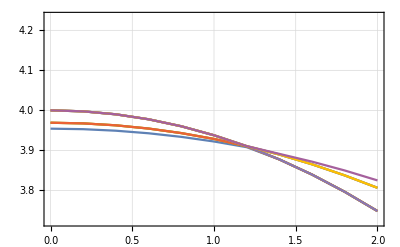

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

3.50199×10^-16

1

0.0000541702

1

0.000216715

1

0.000487738

1

0.000867406

1

0.00135595

1

0.00195368

1

0.00266092

1

0.00347809

1

0.00440563

1

0.00544401

1

0.00659375

1

0.00785538

1

5.90529

1

5.88927

1

5.8719

1

5.85317

1

5.83312

1

5.81178

1

5.78917

1

5.76536

2

2.

2

1.99991

2

1.99962

2

1.99915

2

1.99849

2

1.99764

2

1.99659

2

1.99534

2

1.99389

2

1.99224

2

1.99038

2

1.98831

2

5.91996

2

5.90529

2

5.88927

2

5.8719

2

5.85317

2

5.83312

2

5.81178

2

5.78917

2

5.76536

3

2.

3

1.99991

3

1.99962

3

1.99915

3

1.99849

3

1.99764

3

1.99659

3

1.99534

3

1.99389

3

1.99224

3

1.99038

3

1.98831

3

5.91996

3

5.90529

3

5.88927

3

5.8719

3

5.85317

3

5.83312

3

5.81178

3

5.78917

3

5.76536

4

2.

4

1.99991

4

1.99962

4

1.99915

4

1.99849

4

1.99764

4

1.99659

4

1.99534

4

1.99389

4

1.99224

4

1.99038

4

1.98831

4

5.91996

4

5.90529

4

5.88927

4

5.8719

4

5.85317

4

5.83312

4

5.81178

4

5.78917

4

5.76536

5

6.

5

5.99948

5

5.99791

5

5.99529

5

5.99159

5

5.98679

5

5.98087

5

5.9738

5

5.96554

5

5.95606

5

5.94533

5

5.9333

5

5.91996

5

5.90529

5

5.88927

5

5.8719

5

5.85317

5

5.83312

5

5.81178

5

5.78917

5

5.76536

6

6.

6

5.99948

6

5.99791

6

5.99529

6

5.99159

6

5.98679

6

5.98087

6

5.9738

6

5.96554

6

5.95606

6

5.94533

6

5.9333

6

5.91996

6

0.00922942

6

1.98077

6

1.9778

6

1.97459

6

1.97113

6

1.96743

6

1.96348

6

1.95926

7

6.

7

5.99948

7

5.99791

7

5.99529

7

5.99159

7

5.98679

7

5.98087

7

5.9738

7

5.96554

7

5.95606

7

5.94533

7

5.9333

7

1.98602

7

1.98351

7

1.98077

7

1.9778

7

1.97459

7

1.97113

7

1.96743

7

1.96348

7

1.95926

8

6.

8

5.99948

8

5.99791

8

5.99529

8

5.99159

8

5.98679

8

5.98087

8

5.9738

8

5.96554

8

5.95606

8

5.94533

8

5.9333

8

1.98602

8

1.98351

8

1.98077

8

1.9778

8

1.97459

8

1.97113

8

1.96743

8

1.96348

8

1.95926

9

6.

9

5.99948

9

5.99791

9

5.99529

9

5.99159

9

5.98679

9

5.98087

9

5.9738

9

5.96554

9

5.95606

9

5.94533

9

5.9333

9

1.98602

9

1.98351

9

0.0107164

9

0.0123168

9

0.0140312

9

0.01586

9

0.0178034

9

0.019862

9

0.0220358

10

0.75

10

0.749967

10

0.749866

10

0.7497

10

0.749467

10

0.74917

10

0.748809

10

0.748386

10

0.747903

10

0.747361

10

0.746763

10

0.74611

10

0.745406

10

0.744652

10

0.743852

10

0.743009

10

0.742126

10

0.741205

10

0.74025

10

0.739264

10

0.73825

```mathematica
data1//MatrixForm
```

(1 | 0. | 3.50199×10^-16 | 3.95423
1 | 0.1 | 0.0000541702 | 3.95391
1 | 0.2 | 0.000216715 | 3.95295
1 | 0.3 | 0.000487738 | 3.95135
1 | 0.4 | 0.000867406 | 3.94911
1 | 0.5 | 0.00135595 | 3.94623
1 | 0.6 | 0.00195368 | 3.94271
1 | 0.7 | 0.00266092 | 3.93854
1 | 0.8 | 0.00347809 | 3.93373
1 | 0.9 | 0.00440563 | 3.92827
1 | 1. | 0.00544401 | 3.92216
1 | 1.1 | 0.00659375 | 3.91541
1 | 1.2 | 0.00785538 | 3.908
1 | 1.3 | 5.90529 | 3.89437
1 | 1.4 | 5.88927 | 3.87734
1 | 1.5 | 5.8719 | 3.85903
1 | 1.6 | 5.85317 | 3.83943
1 | 1.7 | 5.83312 | 3.81854
1 | 1.8 | 5.81178 | 3.79638
1 | 1.9 | 5.78917 | 3.77295
1 | 2. | 5.76536 | 3.74826
2 | 0. | 2. | 3.96906
2 | 0.1 | 1.99991 | 3.96866
2 | 0.2 | 1.99962 | 3.96744
2 | 0.3 | 1.99915 | 3.96542
2 | 0.4 | 1.99849 | 3.96259
2 | 0.5 | 1.99764 | 3.95895
2 | 0.6 | 1.99659 | 3.9545
2 | 0.7 | 1.99534 | 3.94923
2 | 0.8 | 1.99389 | 3.94316
2 | 0.9 | 1.99224 | 3.93627
2 | 1. | 1.99038 | 3.92856
2 | 1.1 | 1.98831 | 3.92004
2 | 1.2 | 5.91996 | 3.9101
2 | 1.3 | 5.90529 | 3.89437
2 | 1.4 | 5.88927 | 3.87734
2 | 1.5 | 5.8719 | 3.85903
2 | 1.6 | 5.85317 | 3.83943
2 | 1.7 | 5.83312 | 3.81854
2 | 1.8 | 5.81178 | 3.79638
2 | 1.9 | 5.78917 | 3.77295
2 | 2. | 5.76536 | 3.74826
3 | 0. | 2. | 3.96906
3 | 0.1 | 1.99991 | 3.96866
3 | 0.2 | 1.99962 | 3.96744
3 | 0.3 | 1.99915 | 3.96542
3 | 0.4 | 1.99849 | 3.96259
3 | 0.5 | 1.99764 | 3.95895
3 | 0.6 | 1.99659 | 3.9545
3 | 0.7 | 1.99534 | 3.94923
3 | 0.8 | 1.99389 | 3.94316
3 | 0.9 | 1.99224 | 3.93627
3 | 1. | 1.99038 | 3.92856
3 | 1.1 | 1.98831 | 3.92004
3 | 1.2 | 5.91996 | 3.9101
3 | 1.3 | 5.90529 | 3.89437
3 | 1.4 | 5.88927 | 3.87734
3 | 1.5 | 5.8719 | 3.85903
3 | 1.6 | 5.85317 | 3.83943
3 | 1.7 | 5.83312 | 3.81854
3 | 1.8 | 5.81178 | 3.79638
3 | 1.9 | 5.78917 | 3.77295
3 | 2. | 5.76536 | 3.74826
4 | 0. | 2. | 3.96906
4 | 0.1 | 1.99991 | 3.96866
4 | 0.2 | 1.99962 | 3.96744
4 | 0.3 | 1.99915 | 3.96542
4 | 0.4 | 1.99849 | 3.96259
4 | 0.5 | 1.99764 | 3.95895
4 | 0.6 | 1.99659 | 3.9545
4 | 0.7 | 1.99534 | 3.94923
4 | 0.8 | 1.99389 | 3.94316
4 | 0.9 | 1.99224 | 3.93627
4 | 1. | 1.99038 | 3.92856
4 | 1.1 | 1.98831 | 3.92004
4 | 1.2 | 5.91996 | 3.9101
4 | 1.3 | 5.90529 | 3.89437
4 | 1.4 | 5.88927 | 3.87734
4 | 1.5 | 5.8719 | 3.85903
4 | 1.6 | 5.85317 | 3.83943
4 | 1.7 | 5.83312 | 3.81854
4 | 1.8 | 5.81178 | 3.79638
4 | 1.9 | 5.78917 | 3.77295
4 | 2. | 5.76536 | 3.74826
5 | 0. | 6. | 4.
5 | 0.1 | 5.99948 | 3.99938
5 | 0.2 | 5.99791 | 3.99753
5 | 0.3 | 5.99529 | 3.99443
5 | 0.4 | 5.99159 | 3.99009
5 | 0.5 | 5.98679 | 3.98451
5 | 0.6 | 5.98087 | 3.97767
5 | 0.7 | 5.9738 | 3.96958
5 | 0.8 | 5.96554 | 3.96023
5 | 0.9 | 5.95606 | 3.94961
5 | 1. | 5.94533 | 3.93772
5 | 1.1 | 5.9333 | 3.92455
5 | 1.2 | 5.91996 | 3.9101
5 | 1.3 | 5.90529 | 3.89437
5 | 1.4 | 5.88927 | 3.87734
5 | 1.5 | 5.8719 | 3.85903
5 | 1.6 | 5.85317 | 3.83943
5 | 1.7 | 5.83312 | 3.81854
5 | 1.8 | 5.81178 | 3.79638
5 | 1.9 | 5.78917 | 3.77295
5 | 2. | 5.76536 | 3.74826
6 | 0. | 6. | 4.
6 | 0.1 | 5.99948 | 3.99938
6 | 0.2 | 5.99791 | 3.99753
6 | 0.3 | 5.99529 | 3.99443
6 | 0.4 | 5.99159 | 3.99009
6 | 0.5 | 5.98679 | 3.98451
6 | 0.6 | 5.98087 | 3.97767
6 | 0.7 | 5.9738 | 3.96958
6 | 0.8 | 5.96554 | 3.96023
6 | 0.9 | 5.95606 | 3.94961
6 | 1. | 5.94533 | 3.93772
6 | 1.1 | 5.9333 | 3.92455
6 | 1.2 | 5.91996 | 3.9101
6 | 1.3 | 0.00922942 | 3.89993
6 | 1.4 | 1.98077 | 3.88956
6 | 1.5 | 1.9778 | 3.87776
6 | 1.6 | 1.97459 | 3.86514
6 | 1.7 | 1.97113 | 3.85169
6 | 1.8 | 1.96743 | 3.83742
6 | 1.9 | 1.96348 | 3.82232
6 | 2. | 1.95926 | 3.8064
7 | 0. | 6. | 4.
7 | 0.1 | 5.99948 | 3.99938
7 | 0.2 | 5.99791 | 3.99753
7 | 0.3 | 5.99529 | 3.99443
7 | 0.4 | 5.99159 | 3.99009
7 | 0.5 | 5.98679 | 3.98451
7 | 0.6 | 5.98087 | 3.97767
7 | 0.7 | 5.9738 | 3.96958
7 | 0.8 | 5.96554 | 3.96023
7 | 0.9 | 5.95606 | 3.94961
7 | 1. | 5.94533 | 3.93772
7 | 1.1 | 5.9333 | 3.92455
7 | 1.2 | 1.98602 | 3.9107
7 | 1.3 | 1.98351 | 3.90054
7 | 1.4 | 1.98077 | 3.88956
7 | 1.5 | 1.9778 | 3.87776
7 | 1.6 | 1.97459 | 3.86514
7 | 1.7 | 1.97113 | 3.85169
7 | 1.8 | 1.96743 | 3.83742
7 | 1.9 | 1.96348 | 3.82232
7 | 2. | 1.95926 | 3.8064
8 | 0. | 6. | 4.
8 | 0.1 | 5.99948 | 3.99938
8 | 0.2 | 5.99791 | 3.99753
8 | 0.3 | 5.99529 | 3.99443
8 | 0.4 | 5.99159 | 3.99009
8 | 0.5 | 5.98679 | 3.98451
8 | 0.6 | 5.98087 | 3.97767
8 | 0.7 | 5.9738 | 3.96958
8 | 0.8 | 5.96554 | 3.96023
8 | 0.9 | 5.95606 | 3.94961
8 | 1. | 5.94533 | 3.93772
8 | 1.1 | 5.9333 | 3.92455
8 | 1.2 | 1.98602 | 3.9107
8 | 1.3 | 1.98351 | 3.90054
8 | 1.4 | 1.98077 | 3.88956
8 | 1.5 | 1.9778 | 3.87776
8 | 1.6 | 1.97459 | 3.86514
8 | 1.7 | 1.97113 | 3.85169
8 | 1.8 | 1.96743 | 3.83742
8 | 1.9 | 1.96348 | 3.82232
8 | 2. | 1.95926 | 3.8064
9 | 0. | 6. | 4.
9 | 0.1 | 5.99948 | 3.99938
9 | 0.2 | 5.99791 | 3.99753
9 | 0.3 | 5.99529 | 3.99443
9 | 0.4 | 5.99159 | 3.99009
9 | 0.5 | 5.98679 | 3.98451
9 | 0.6 | 5.98087 | 3.97767
9 | 0.7 | 5.9738 | 3.96958
9 | 0.8 | 5.96554 | 3.96023
9 | 0.9 | 5.95606 | 3.94961
9 | 1. | 5.94533 | 3.93772
9 | 1.1 | 5.9333 | 3.92455
9 | 1.2 | 1.98602 | 3.9107
9 | 1.3 | 1.98351 | 3.90054
9 | 1.4 | 0.0107164 | 3.89121
9 | 1.5 | 0.0123168 | 3.88183
9 | 1.6 | 0.0140312 | 3.87178
9 | 1.7 | 0.01586 | 3.86107
9 | 1.8 | 0.0178034 | 3.8497
9 | 1.9 | 0.019862 | 3.83765
9 | 2. | 0.0220358 | 3.82493
10 | 0. | 0.75 | 4.95407
10 | 0.1 | 0.749967 | 4.95344
10 | 0.2 | 0.749866 | 4.95155
10 | 0.3 | 0.7497 | 4.9484
10 | 0.4 | 0.749467 | 4.94399
10 | 0.5 | 0.74917 | 4.93833
10 | 0.6 | 0.748809 | 4.93141
10 | 0.7 | 0.748386 | 4.92324
10 | 0.8 | 0.747903 | 4.91382
10 | 0.9 | 0.747361 | 4.90316
10 | 1. | 0.746763 | 4.89126
10 | 1.1 | 0.74611 | 4.87813
10 | 1.2 | 0.745406 | 4.86377
10 | 1.3 | 0.744652 | 4.84819
10 | 1.4 | 0.743852 | 4.83139
10 | 1.5 | 0.743009 | 4.81339
10 | 1.6 | 0.742126 | 4.79418
10 | 1.7 | 0.741205 | 4.77378
10 | 1.8 | 0.74025 | 4.7522
10 | 1.9 | 0.739264 | 4.72944
10 | 2. | 0.73825 | 4.70552)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;13,1;;4]];
tmp02 = data1[[119;;119,1;;4]];
tmp03 = data1[[183;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;33,1;;4]];
tmp02 = data1[[160;;168, 1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.95423 | 3.50199×10^-16
0.1 | 3.95391 | 0.0000541702
0.2 | 3.95295 | 0.000216715
0.3 | 3.95135 | 0.000487738
0.4 | 3.94911 | 0.000867406
0.5 | 3.94623 | 0.00135595
0.6 | 3.94271 | 0.00195368
0.7 | 3.93854 | 0.00266092
0.8 | 3.93373 | 0.00347809
0.9 | 3.92827 | 0.00440563
1. | 3.92216 | 0.00544401
1.1 | 3.91541 | 0.00659375
1.2 | 3.908 | 0.00785538
1.3 | 3.89993 | 0.00922942
1.4 | 3.89121 | 0.0107164
1.5 | 3.88183 | 0.0123168
1.6 | 3.87178 | 0.0140312
1.7 | 3.86107 | 0.01586
1.8 | 3.8497 | 0.0178034
1.9 | 3.83765 | 0.019862
2. | 3.82493 | 0.0220358)

(0. | 3.96906 | 2.
0.1 | 3.96866 | 1.99991
0.2 | 3.96744 | 1.99962
0.3 | 3.96542 | 1.99915
0.4 | 3.96259 | 1.99849
0.5 | 3.95895 | 1.99764
0.6 | 3.9545 | 1.99659
0.7 | 3.94923 | 1.99534
0.8 | 3.94316 | 1.99389
0.9 | 3.93627 | 1.99224
1. | 3.92856 | 1.99038
1.1 | 3.92004 | 1.98831
1.2 | 3.9107 | 1.98602
1.3 | 3.90054 | 1.98351
1.4 | 3.88956 | 1.98077
1.5 | 3.87776 | 1.9778
1.6 | 3.86514 | 1.97459
1.7 | 3.85169 | 1.97113
1.8 | 3.83742 | 1.96743
1.9 | 3.82232 | 1.96348
2. | 3.8064 | 1.95926)

(0. | 4. | 6.
0.1 | 3.99938 | 5.99948
0.2 | 3.99753 | 5.99791
0.3 | 3.99443 | 5.99529
0.4 | 3.99009 | 5.99159
0.5 | 3.98451 | 5.98679
0.6 | 3.97767 | 5.98087
0.7 | 3.96958 | 5.9738
0.8 | 3.96023 | 5.96554
0.9 | 3.94961 | 5.95606
1. | 3.93772 | 5.94533
1.1 | 3.92455 | 5.9333
1.2 | 3.9101 | 5.91996
1.3 | 3.89437 | 5.90529
1.4 | 3.87734 | 5.88927
1.5 | 3.85903 | 5.8719
1.6 | 3.83943 | 5.85317
1.7 | 3.81854 | 5.83312
1.8 | 3.79638 | 5.81178
1.9 | 3.77295 | 5.78917
2. | 3.74826 | 5.76536)

```mathematica
|
```

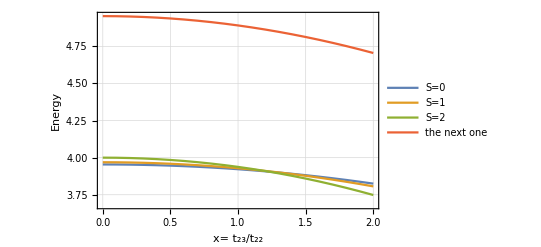

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

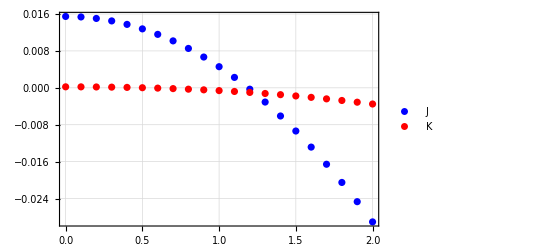

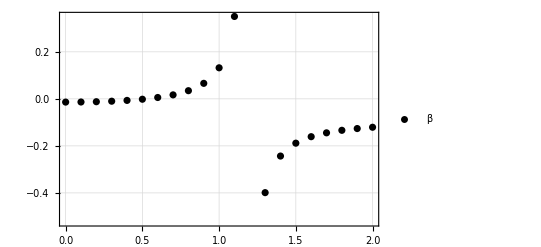

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```